## Load Package

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
```

## Prepare default user data

This needs to be done whenever there is a code change to the underlying EntityStores.

### Default “MyFood” EntityStore

#### Create new entity store from scratch (Old, loses data)

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
EntityUnregister["MyFood"]
Internal`ClearEntityValueCache["MyFood"]
AbsoluteTiming[store=GenerateEntityStore[CloudObject["MealTracker_2-23-2018"],"MyFood",{"white bread", "peanut butter", "jelly","milk","oats","greek yogurt","flax seed","honey","vanilla extract"}];]
EntityRegister[store]
```

{21.2963,Null}

{MyFood}

#### Create new EntityStore from an old EntityStore (Preferred, keeps data)

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
```

```mathematica
LoadEntityStore[CloudObject["MealTracker_2-23-2018"],"MyFood"]
```

{MyFood}

```mathematica
oldStore=Entity["MyFood"]["EntityStore"];
```

```mathematica
oldEntityData=oldStore[[1,"Types","MyFood","Entities"]];
oldEntityData//Keys
```

{WhiteBread,PeanutButter,Jelly,Milk,GreekYogurt,FlaxSeed,Honey,VanillaExtract,Egg,CanolaOil,GranulatedSugar,Applesauce,GroundCinnamon,ArgoDoubleActingAluminiumFreeBakingPowder,QuakerOatsOldFashioned,KraftPhiladelphiaOriginalCreamCheese,C&HPureCaneSugar,OrangeJuice,Kefir,MontereyJackCheese,EnglishMuffin,YorkPeppermintPatty,Cheez-Its,MortonIodizedSalt,FrozenStrawberries,Bread,Wheat,Sprouted,Cheese,Goat,SemisoftType,CherryTomatoes,Chickpeas(garbanzoBeans,BengalGram),MatureSeeds,Canned,SolidsAndLiquids,LowSodium,Spices,Basil,Dried,OliveOil,RefriedBeans,Banana,MapleSyrup,RefriedBeans3,NabiscoRitzCrackers,TrefoilCookies,Shallot,GingerRoot,Garlic,Turmeric,Cumin,CurryPaste,Kale,Raw,CoconutMilk,BrownSugar,Tofu,SweetPotato,LimeJuice,Spaghetti,ClifBarEnergyBarBlueberryCrisp,PizzaHutPepperoniPizza,PizzaHutBreadsticks,PepperidgeFarmWholeGrainBread,Watermelon,HashBrowns,CreamOfChickenSoup,SourCream,YellowOnion,ColbyCheese,CornFlakes,Butter,Pancakes,Blueberries,Raw,TortillaChips,Salsa,ChocolateChips,Apples,Raw,GrannySmith,WithSkin,WhiteChocolateCoveredPretzels,Cheeseburger,MashedPotatoes,HamAndCheeseOmelet,CarnitasBurrito,QuesoSauce,AlmondMilk,Couscous,FrozenChicken,GreekSalad,HoneyBarbecueSauce,SilverDollarHashBrowns,StrawberryRechargeSmoothieWithProteinPowder}

#### Update basic data for test deployments (OPTIONAL)

```mathematica
newBasicData=Join[
oldEntityData[[;;9]],
<|"Oats"-><|"Label"->"Oats","Food"->Entity["Food","QuakerOatsOldFashioned::8t545"],"ServingSizeString"->"0.5 cup;40. g","ServingSizes"->{Quantity[0.5, "Cups"],Quantity[40., "Grams"]},"Description"->"Oats","ServingSize"->"0.5 cup;40. g","TotalCalories"->Quantity[150., "LargeCalories"],"Calcium"->Quantity[0., "Milligrams"],"Cholesterol"->Quantity[0., "Milligrams"],"Iron"->Quantity[1.8, "Milligrams"],"Sodium"->Quantity[0., "Milligrams"],"TotalCarbohydrates"->Quantity[27., "Grams"],"TotalFat"->Quantity[3., "Grams"],"TotalFiber"->Missing["NoInput"],"TotalProtein"->Quantity[5., "Grams"],"TotalSaturatedFat"->Quantity[0.5, "Grams"],"VitaminC"->Quantity[0., "Milligrams"],"Resubmit"->True,"Entity"->Entity["Food","QuakerOatsOldFashioned::8t545"],"DateCreated"->DateObject[{2018,3,29,11,57,46.197763`8.417195923159113},"Instant","Gregorian",-5.],"DateModified"->DateObject[{2018,3,29,11,57,46.198024`8.4171983767528},"Instant","Gregorian",-5.]|>|>
];
```

```mathematica
cleanerBasicData=RotateLeft[Prepend[#,"DateCreated"->Lookup[#,"DateCreated",Lookup[#,"DateModified",Now]]]]&/@(KeyDrop[{"Description","ServingSize","Entity"}]/@newBasicData);
```

```mathematica
(* Use this to create a new data file for updating the default *)
SetDirectory[FileNameJoin[{NotebookDirectory[],"Default","MyFood"}]]
Export[StringReplace[DateString["ISODateTime"],{"T"->"_",":"->"-"}]<>".m",
cleanerBasicData
]
```

C:\Users\andrews\Stash\open-source-meal-tracking\MealTrackerApp\Default\MyFood

2018-04-23_13-25-38.m

#### Fix extra information floating around in PRD data (OPTIONAL)

```mathematica
fixedEntityData=RotateLeft[Prepend[#,"DateCreated"->Lookup[#,"DateCreated",Lookup[#,"DateModified",Now]]]]&/@Append[oldEntityData,"Oats"-><|"Label"->"Oats","Food"->Entity["Food","QuakerOatsOldFashioned::8t545"],"ServingSizeString"->"0.5 cup;40. g","ServingSizes"->{Quantity[0.5, "Cups"],Quantity[40., "Grams"]},"Description"->"Oats","ServingSize"->"0.5 cup;40. g","TotalCalories"->Quantity[150., "LargeCalories"],"Calcium"->Quantity[0., "Milligrams"],"Cholesterol"->Quantity[0., "Milligrams"],"Iron"->Quantity[1.8, "Milligrams"],"Sodium"->Quantity[0., "Milligrams"],"TotalCarbohydrates"->Quantity[27., "Grams"],"TotalFat"->Quantity[3., "Grams"],"TotalFiber"->Missing["NoInput"],"TotalProtein"->Quantity[5., "Grams"],"TotalSaturatedFat"->Quantity[0.5, "Grams"],"VitaminC"->Quantity[0., "Milligrams"],"Resubmit"->True,"Entity"->Entity["Food","QuakerOatsOldFashioned::8t545"],"DateCreated"->DateObject[{2018,3,29,11,57,46.197763`8.417195923159113},"Instant","Gregorian",-5.],"DateModified"->DateObject[{2018,3,29,11,57,46.198024`8.4171983767528},"Instant","Gregorian",-5.]|>];
```

#### Test EntityStore

```mathematica
EntityUnregister["MyFood"]
Internal`ClearEntityValueCache["MyFood"]
AbsoluteTiming[store=GenerateEntityStore[CloudObject["MealTracker_2-23-2018"],"MyFood",oldEntityData];]
EntityRegister[store]
```

{0.145888,Null}

{MyFood}

```mathematica
EntityValue["MyFood","EntityCount"]
```

82

#### Update EntityStore in cloud

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
```

```mathematica
UpdateEntityStore[CloudObject["MealTracker_2-23-2018"],"MyFood",store]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/MyFood/2018-04-23_14-06-09.WXF]

```mathematica
LoadEntityStore[CloudObject["MealTracker_2-23-2018"],"MyFood"]
```

{MyFood}

```mathematica
EntityValue["MyFood","EntityCount"]
```

82

### Default “MyMeal” EntityStore

#### Create new EntityStore from scratch (Old, loses data)

This loads from the latest file in MealTrackerApp/Default/MyMeal/

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
EntityUnregister["MyMeal"]
Internal`ClearEntityValueCache["MyMeal"]
AbsoluteTiming[mealStore=GenerateEntityStore[CloudObject["MealTracker_2-23-2018"],"MyMeal"];]
EntityRegister[mealStore]
```

{0.580319,Null}

{MyMeal}

#### Create new EntityStore from an old EntityStore (Preferred, keeps data)

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
```

```mathematica
LoadEntityStore[CloudObject["MealTracker_2-23-2018"],"MyMeal"]
```

{MyMeal}

```mathematica
oldStore=Entity["MyMeal"]["EntityStore"];
```

```mathematica
oldEntityData=oldStore[[1,"Types","MyMeal","Entities"]];
oldEntityData//Keys
```

{PB&JSandwich,OvernightOats,CakeBatterOvernightOats,CakeBatterOvernightOats2,EggSandwich,PanangCurry,FuneralPotatoes,AnotherTestMeal,TestMeal#3,PeanutButterOvernightOats,PeanutButterAndBananaOvernightOats,TestMeal#4}

```mathematica
EntityUnregister["MyMeal"]
Internal`ClearEntityValueCache["MyMeal"]
AbsoluteTiming[mealStore=GenerateEntityStore[CloudObject["MealTracker_2-23-2018"],"MyMeal",oldEntityData];]
EntityRegister[mealStore]
```

{0.142065,Null}

{MyMeal}

```mathematica
EntityValue[Entity["MyMeal","PeanutButterOvernightOats"],"Calcium"]
```

169.765 mg

```mathematica
LogMeal[CloudObject["https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018"],Entity["MyMeal","EggSandwich"],1,"Breakfast",<|"Year"->2018,"Month"->4,"Day"->23,"Hour"->9|>]
```

Databin[…]

#### Update EntityStore in cloud

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
```

```mathematica
UpdateEntityStore[CloudObject["MealTracker_2-23-2018"],"MyMeal",mealStore]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/MyMeal/2018-04-23_14-20-32.WXF]

## Run tests

### Deployment and full-system tests

```mathematica
CloudConnect[]
SetDirectory[NotebookDirectory[]];
AbsoluteTiming[results=TestReport["MealTrackerApp.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

#### Visualize timing results

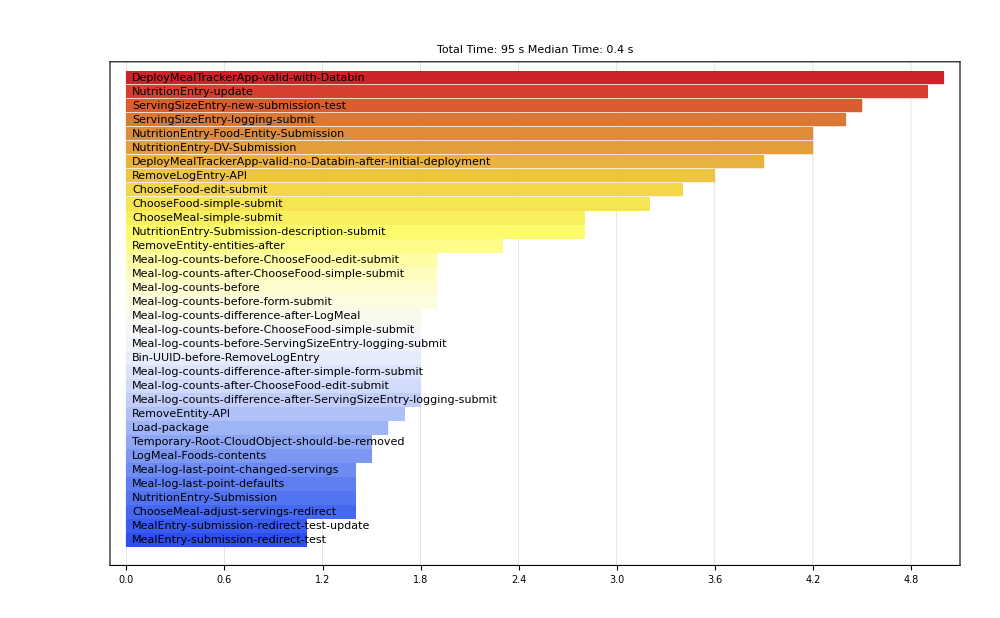

```mathematica
times=KeySelect[Association[#["TestID"]-> #["AbsoluteTimeUsed"]&/@Values[results["TestResults"]]],MatchQ[_String]];
appreciableTimes=Sort[times]//Select[#>Quantity[1,"Seconds"]&];
appreciableTimes=Round[#,0.1]&/@appreciableTimes;
BarChart[appreciableTimes,
BarOrigin->Left,
ImageSize->1000,
ChartLabels->Placed[Style[#,Black]&/@Keys[appreciableTimes],Left],
PlotTheme->"Detailed",
ChartStyle->"TemperatureMap",
PlotLabel->StringTemplate["Total Time: `` \nMedian Time: ``"][Round@Total[times],Round[Median[times],0.1]]
]
```

### General Utility tests

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Utilities"}]];
AbsoluteTiming[results=TestReport["General.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

{9.18881,TestReportObject[…]}

### EntityStore Utility tests

TODO: This test suite requires that the main package be loaded!

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Utilities"}]];
AbsoluteTiming[results=TestReport["EntityStore.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

{0.914506,TestReportObject[…]}

### GenerateData tests

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Utilities"}]];
AbsoluteTiming[results=TestReport["GenerateData.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

{16.8573,TestReportObject[…]}

### RadarPlot tests

```mathematica
SetDirectory[NotebookDirectory[]];
AbsoluteTiming[results=TestReport["Plots/RadarPlot.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

{1.66331,TestReportObject[…]}

### NutritionRadarPlot tests

```mathematica
SetDirectory[NotebookDirectory[]];
AbsoluteTiming[results=TestReport["Plots/NutritionRadarPlot.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

{1.22662,TestReportObject[…]}

## Deploy App to cloud

### Re-deploy and overwrite all data

#### Create a databin

```mathematica
Databin;
DataDropClient`$JavaCompatibleQ=False;
bin=CreateDatabin["Name" -> "Meal Tracker 2/23/2018 #3"]
```

Databin[…]

#### Redeploy

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
(* Created 3/29/18 *)
bin=Databin["ttOfD1G4"];
Print["Copying entity stores to disk..."];
If[Not@DirectoryQ["MyFood_History"],CreateDirectory["MyFood_History"]];
If[Not@DirectoryQ["MyMeal_History"],CreateDirectory["MyMeal_History"]];
CopyFile[#,FileNameJoin[{"MyFood_History",FileNameTake[First@#]}]]&/@CloudObjects[FileNameJoin[{CloudObject["MealTracker_2-23-2018"],"MyFood"}]];
CopyFile[#,FileNameJoin[{"MyMeal_History",FileNameTake[First@#]}]]&/@CloudObjects[FileNameJoin[{CloudObject["MealTracker_2-23-2018"],"MyMeal"}]];
Print["Deploying app..."];
DeployMealTrackerApp[CloudObject["MealTracker_2-23-2018"],"DefaultDirectory"->Automatic,"HistoryDatabin"->bin,"OverwriteExistingData"->True]
```

Copying entity stores to disk...

Deploying app...

{CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/Home],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/MealEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ServingSizeEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/NutritionEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewFood],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewMeal],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ChooseMeal],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ChooseFood],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewHistory],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/RemoveLogEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodSearch],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodLookup],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/RemoveEntity]}

### Copy EntityStores

```mathematica
CopyFile["C:\\Users\\andrews\\Stash\\open-source-meal-tracking\\MealTrackerApp\\MyFood_History\\2018-03-20_16-22-06.WXF",CloudObject["MealTracker_2-23-2018/MyFood/2018-03-20_16-22-06.WXF"]]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/MyFood/2018-03-20_16-22-06.WXF]

```mathematica
CopyFile["C:\\Users\\andrews\\Stash\\open-source-meal-tracking\\MealTrackerApp\\MyMeal_History\\2018-03-20_16-11-39.WXF",CloudObject["MealTracker_2-23-2018/MyMeal/2018-03-20_16-11-39.WXF"]]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/MyMeal/2018-03-20_16-11-39.WXF]

### Re-deploy without changing EntityStore data

```mathematica
CloudConnect[]
```

andrews@wolfram.com

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
DeployMealTrackerApp[CloudObject["MealTracker_2-23-2018"],"DefaultDirectory"->Automatic]
%[[-1]]//SystemOpen
```

{CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/Home],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/MealEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ServingSizeEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/NutritionEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewFood],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewMeal],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ChooseMeal],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ChooseFood],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewHistory],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/RemoveLogEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodSearch],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodLookup],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/RemoveEntity],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ServingSizeMultiplication],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/Settings],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/Reminders],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ScanBarcode],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/Suggestion]}

### Load EntityStores for debugging purposes

```mathematica
LoadEntityStore[CloudObject["MealTracker_2-23-2018"],"MyFood"]//AbsoluteTiming
LoadEntityStore[CloudObject["MealTracker_2-23-2018"],"MyMeal"]//AbsoluteTiming
```

{0.407144,{MyFood}}

{0.254044,{MyMeal}}

## Suggestion scratchwork

### Test solution on old data

```mathematica
SetDirectory[NotebookDirectory[]];
dinnerData=Import["DinnerData.m"];
```

```mathematica
ranges=({1,0}+#)&/@Partition[Insert[Accumulate[Values[Length/@Reverse[dinnerData]]],0,1],2,1]
```

{{1,54},{55,64},{65,72}}

```mathematica
NSolve[6*x==72]
```

{{x→12.}}

```mathematica
Length@dinnerData[[1,1]]
```

7

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
With[
{
nutritionTargets=<|"TotalCalories"->2000,"TotalFat"->65,"TotalProtein"->50,"TotalCarbohydrates"->300,"TotalSugar"->50,"VitaminC"->65|>,
nutritionRemaining=<|"TotalCalories"->600,"TotalFat"->20,"TotalProtein"->30,"TotalCarbohydrates"->60,"TotalSugar"->21,"VitaminC"->15|>
},
Utilities`Suggestion`Private`findDinner[
1.,
(* Consumed so far *)
(nutritionTargets-nutritionRemaining),
nutritionTargets,
QuantityMagnitude[dinnerData],
0.2
]
]
```

72

6

Length 72

{EntityGroup[{EntityInstance[Chicken, skin (drumsticks and thighs), enhanced, raw,1 serving],EntityInstance[Lima beans, large, mature seeds, cooked, boiled, with salt,1 serving],EntityInstance[Broccoli raab, raw,1 serving]}]}

```mathematica
dinnerData[[;;1,;;5]]
```

<|Vegetable→<|BroccoliRaabRaw::j5npy→<|ServingSize→40. g,TotalCalories→8.8 Cal,TotalFat→0.196 g,TotalProtein→1.268 g,TotalCarbohydrates→1.14 g,TotalSugar→0.152 g,VitaminC→8.08 mg|>,BrusselsSproutsFrozenCookedBoiledDrainedWithoutSalt::ctr3w→<|ServingSize→155. g,TotalCalories→65.1 Cal,TotalFat→0.6045 g,TotalProtein→5.642 g,TotalCarbohydrates→12.896 g,TotalSugar→3.224 g,VitaminC→70.835 mg|>,FennelBulbRaw::6f94h→<|ServingSize→87. g,TotalCalories→26.97 Cal,TotalFat→0.174 g,TotalProtein→1.0788 g,TotalCarbohydrates→6.351 g,TotalSugar→3.4191 g,VitaminC→10.44 mg|>,KaleFrozenCookedBoiledDrainedWithSalt::f7vdq→<|ServingSize→130. g,TotalCalories→39. Cal,TotalFat→0.637 g,TotalProtein→3.692 g,TotalCarbohydrates→6.799 g,TotalSugar→1.742 g,VitaminC→32.76 mg|>,KaleRaw::k5b2f→<|ServingSize→16. g,TotalCalories→7.84 Cal,TotalFat→0.1488 g,TotalProtein→0.6848 g,TotalCarbohydrates→1.4 g,TotalSugar→0.3616 g,VitaminC→19.2 mg|>|>|>

### Attempt to recreate data with meals

```mathematica
EntityList["MyMeal"]
```

{PB & J Sandwich,Overnight Oats,Cake Batter Overnight Oats,Cake Batter Overnight Oats 2,Egg Sandwich,Panang Curry,Funeral Potatoes,Another test meal,Test meal #3,Peanut Butter Overnight Oats,Peanut Butter and Banana Overnight Oats,Test Meal #4,Cinnamon Bun Overnight Oats,Cheddar Drop Biscuits,Broccoli Cheddar Soup,Mac & Cheese & Soy Crumbles,Cinnamon City Overnight Oats,Spaghetti & Meatballs,Fruitzert,Chilli,Apple Nachos}

```mathematica
mealToTypes=EntityValue["MyMeal","MealTypes","EntityAssociation"]
```

<|PB & J Sandwich→{Lunch},Overnight Oats→{Breakfast},Cake Batter Overnight Oats→{Breakfast},Cake Batter Overnight Oats 2→{Dinner},Egg Sandwich→{Breakfast},Panang Curry→{Dinner},Funeral Potatoes→{Dinner,Lunch},Another test meal→{Lunch},Test meal #3→{Lunch},Peanut Butter Overnight Oats→{Breakfast},Peanut Butter and Banana Overnight Oats→{Breakfast},Test Meal #4→{Lunch},Cinnamon Bun Overnight Oats→{Breakfast},Cheddar Drop Biscuits→{Dinner,Lunch,Snack},Broccoli Cheddar Soup→{Dinner},Mac & Cheese & Soy Crumbles→{Dinner},Cinnamon City Overnight Oats→{Breakfast},Spaghetti & Meatballs→{Dinner},Fruitzert→{Snack},Chilli→{Dinner},Apple Nachos→{Snack}|>

```mathematica
mealTypeToMeals=KeySelect[GroupBy[mealToTypes,Identity,Keys],Length[#]===1&]//KeyMap[First]
```

<|Lunch→{PB & J Sandwich,Another test meal,Test meal #3,Test Meal #4},Breakfast→{Overnight Oats,Cake Batter Overnight Oats,Egg Sandwich,Peanut Butter Overnight Oats,Peanut Butter and Banana Overnight Oats,Cinnamon Bun Overnight Oats,Cinnamon City Overnight Oats},Dinner→{Cake Batter Overnight Oats 2,Panang Curry,Broccoli Cheddar Soup,Mac & Cheese & Soy Crumbles,Spaghetti & Meatballs,Chilli},Snack→{Fruitzert,Apple Nachos}|>

```mathematica
mealToNutrition=EntityValue["MyMeal","NutritionAssociation","EntityAssociation"];
```

```mathematica
typeToMealNutrition=DeleteMissing[KeyTake[mealToNutrition,#],1,2]&/@mealTypeToMeals;
typeToMealNutrition=Map[KeyDrop["TotalFiber"],typeToMealNutrition,{2}];
```

### Reproduce both methods after refactoring

Things that can be done:
1. Suggest meals for a whole day.
2. Suggest individual meals for a given day
Breakfast & Lunch #1: Estimate other contributions, solve using difference.
Dinner: Use as MTrott originally intended (but only one category using difference).
TODO: Modify to allow multiples in single-meal case.

Easy solution: Solve for whole day, only report meals asked for (kind of cheating, but works)

#### MTrott’s solution

How to suggest breakfast:
1. Estimate remaining dinner contributions from history.

Breakfast:
Estimate lunch and dinner contribution from history. If not known, Breakfast -> 400, Lunch -> 600, Dinner -> 600 (or Breakfast ->600 for me, Lunch -> 50%, Dinner -> 50%).
Subtract from targets, this is the new remaining amount to satisfy.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
With[
{
nutritionTargets=<|"TotalCalories"->2000(*,"TotalFat"->65,"TotalProtein"->50,"TotalCarbohydrates"->300,"TotalSugar"->50,"VitaminC"->65*)|>,
nutritionRemaining=<|"TotalCalories"->1500(*,"TotalFat"->30,"TotalProtein"->35,"TotalCarbohydrates"->250,"TotalSugar"->10,"VitaminC"->50*)|>
},
Utilities`Suggestion`Private`findDinner[
1,
0.6*nutritionTargets,
nutritionTargets,
QuantityMagnitude[Map[KeyTake[{"TotalCalories"}]]/@Echo@KeyDrop[typeToMealNutrition,{"Lunch","Snack","Dinner"}]],
0.8
]
]
```

<|Breakfast→<|Overnight Oats→<|TotalCalories→1726.66 Cal,Calcium→530.802 mg,Cholesterol→35.5 mg,Iron→7.72884 mg,Sodium→199.438 mg,TotalCarbohydrates→366.67 g,TotalFat→21.3025 g,TotalProtein→38.022 g,TotalSaturatedFat→5.63442 g,VitaminC→2.895 mg|>,Cake Batter Overnight Oats→<|TotalCalories→318.536 Cal,Calcium→198.81 mg,Cholesterol→15.125 mg,Iron→2.31437 mg,Sodium→76.4847 mg,TotalCarbohydrates→49.2877 g,TotalFat→7.24419 g,TotalProtein→13.2955 g,TotalSaturatedFat→2.45067 g,VitaminC→0.670625 mg|>,Egg Sandwich→<|TotalCalories→294. Cal,Calcium→200.75 mg,Cholesterol→212.5 mg,Iron→1.23 mg,Sodium→474. mg,TotalCarbohydrates→26.9075 g,TotalFat→12.5525 g,TotalProtein→16.39 g,TotalSaturatedFat→6.148 g,VitaminC→0.1 mg|>,Peanut Butter Overnight Oats→<|TotalCalories→683.158 Cal,Calcium→169.765 mg,Cholesterol→12.5 mg,Iron→2.98828 mg,Sodium→272.813 mg,TotalCarbohydrates→79.5831 g,TotalFat→32.4686 g,TotalProtein→22.9718 g,TotalSaturatedFat→7.07267 g,VitaminC→5.2315 mg|>,Peanut Butter and Banana Overnight Oats→<|TotalCalories→718.158 Cal,Calcium→169.765 mg,Cholesterol→12.5 mg,Iron→2.80828 mg,Sodium→202.813 mg,TotalCarbohydrates→94.5843 g,TotalFat→31.9682 g,TotalProtein→20.971 g,TotalSaturatedFat→10.5726 g,VitaminC→5.2315 mg|>,Cinnamon Bun Overnight Oats→<|TotalCalories→757.696 Cal,Calcium→491.897 mg,Cholesterol→51.3733 mg,Iron→4.68315 mg,Sodium→242.125 mg,TotalCarbohydrates→114.54 g,TotalFat→19.0911 g,TotalProtein→33.646 g,TotalSaturatedFat→8.05941 g,VitaminC→1.30594 mg|>,Cinnamon City Overnight Oats→<|TotalCalories→676.138 Cal,Calcium→438.552 mg,Cholesterol→30.25 mg,Iron→4.62922 mg,Sodium→171.468 mg,TotalCarbohydrates→92.9237 g,TotalFat→23.0993 g,TotalProtein→28.7826 g,TotalSaturatedFat→12.0848 g,VitaminC→1.2165 mg|>|>|>

Bounds 160. | 1440.

{0,0,0,1,0,0,0}

{EntityGroup[{EntityInstance[Entity[Food,Peanut Butter Overnight Oats],1 serving]}]}

```mathematica
Entity["MyMeal","CinnamonBunOvernightOats"]["ServingCount"]
```

1

TODO: Try to reduce the amount of data fed into it all? Simplify the problem?

```mathematica
Map[KeyTake[{"TotalCalories"}]]/@typeToMealNutrition
```

<|Lunch→<|PB & J Sandwich→<|TotalCalories→375.86 Cal|>,Test Meal #4→<|TotalCalories→312.483 Cal|>|>,Breakfast→<|Overnight Oats→<|TotalCalories→1726.66 Cal|>,Cake Batter Overnight Oats→<|TotalCalories→318.536 Cal|>,Egg Sandwich→<|TotalCalories→294. Cal|>,Peanut Butter Overnight Oats→<|TotalCalories→683.158 Cal|>,Peanut Butter and Banana Overnight Oats→<|TotalCalories→718.158 Cal|>,Cinnamon Bun Overnight Oats→<|TotalCalories→757.696 Cal|>,Cinnamon City Overnight Oats→<|TotalCalories→676.138 Cal|>|>,Dinner→<|Cake Batter Overnight Oats 2→<|TotalCalories→397.036 Cal|>,Panang Curry→<|TotalCalories→506.158 Cal|>,Broccoli Cheddar Soup→<|TotalCalories→413.097 Cal|>,Mac & Cheese & Soy Crumbles→<|TotalCalories→660.215 Cal|>,Spaghetti & Meatballs→<|TotalCalories→459.9 Cal|>,Chilli→<|TotalCalories→216.332 Cal|>|>,Snack→<|Fruitzert→<|TotalCalories→302.053 Cal|>,Apple Nachos→<|TotalCalories→434.88 Cal|>|>|>

#### MTrott’s solution for all day

This should work just fine, but we may want to have a means of generating “common meals” from foods to add to this.
E.g. full meals that are actually eaten (Egg sandwich + OJ + Banana, Egg sandwich + Milk + banana + Yogurt, etc...)
How to do this:
In data analysis, find most common foods/meals during same meal time.
Then, suggest meals that can be created from them (autopopulate and create these in a menu, give a nice name?)
OR
we just do this programmatically and not show it?

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
With[
{
nutritionTargets=<|"TotalCalories"->2000,"TotalFat"->65,"TotalProtein"->50,"TotalCarbohydrates"->300,"TotalSugar"->50,"VitaminC"->65|>
},
Utilities`Suggestion`Private`findDinner[
1,
0.*nutritionTargets,
nutritionTargets,
QuantityMagnitude[(*Map[KeyTake[{"TotalCalories","TotalFat","TotalProtein"}]]/@*)KeyDrop[typeToMealNutrition,{"Snack","Lunch"}]]//Echo[#,"",Keys]&,
0.5
]
]
```

{Breakfast,Dinner}

{EntityGroup[{EntityInstance[Entity[Food,Egg Sandwich],1 serving],EntityInstance[Entity[Food,Mac & Cheese & Soy Crumbles],1 serving]}]}

#### Another idea

Modify MTrott’s solution to allow 
Breakfast + common Breakfast foods
Lunch + common lunch foods
Dinner + common dinner foods
and solve each one individually

The common dinner foods should be generated from the history (or tags, if we have them)

Then, this should be the ideal solution for now.

#### Yet Another idea

Determine common meals (actually go through the history of what’s been consumed, group all of them, give names).
Then, use MTrott’s solution on those to get all day figured out.

Advantage: Have ready solution for all day, based on history. Gives more options.

#### Dan’s solution (couldn’t quite get it to work)

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
Utilities`Suggestion`Private`selectDinners[Map[KeyTake[{"TotalCalories"}]]/@typeToMealNutrition][
<|"TotalCalories"->1000(*"TotalCarbohydrates"->60*)(*,"TotalFat"->3,"TotalProtein"->55,"TotalSugar"->10,"VitaminC"->12*)|>,
1.5,
1,
N@<|"Protein"->1/3,"Vegetable"->1/3,"Starch"->1/3|>,
<|"TotalCalories"->Quantity[2000.,"LargeCalories"],"TotalFat"->Quantity[80.,"Grams"],"TotalSugar"->Quantity[45.,"Grams"],"TotalCarbohydrates"->Quantity[400.,"Grams"]|>
]
```

{}

## Figure out “effective meals” for suggestion

### Get all history

```mathematica
bin=Databin["ttOfD1G4"];
```

```mathematica
CloudConnect[]
```

andrews@wolfram.com

```mathematica
allData=Normal@Dataset[bin];
```

### Group and clean up into “effective meals”

```mathematica
groupedData=GroupBy[allData,{#MealType&->KeyDrop["MealType"],DateObject[Take[DateList[#Timestamp],3]]&->KeyDrop["Timestamp"]}];
```

```mathematica
mealTypeToEffectiveMeals=Values/@Map[
Flatten[#[[All,"Meal"]]]->N[Total[KeyDrop[#,{"Meal","TotalFiber"}]]/._Missing->0]&,
groupedData,
{2}
];
```

```mathematica
mealToNutritionData=Join@@Values[mealTypeToEffectiveMeals];
```

```mathematica
ClearAll[myTotal];
myTotal[l:{Quantity[_?NumberQ,_]..}]:=Total[l/.{("Cups"*"Servings"|"Servings"*"Slices")->"Servings","Servings"*"Tablespoons"->"Tablespoons","Pieces"*"Servings"->"Pieces"}];

normalizeEffectiveMeal=Replace[x:{EntityInstance[y_,_]..}:>EntityInstance[y,myTotal[x[[All,2]]]]]/@Values[GroupBy[#,Replace[#,EntityInstance[a_,___]:>a]&]]&;
effectiveMealToNutrition=KeyMap[Flatten,GroupBy[mealToNutritionData,normalizeEffectiveMeal[First[#]]&->Last,First]];
```

```mathematica
effectiveMealToNutrition//Length
```

90

```mathematica
mealTypeToEffectiveMealNutrition=KeyTake[effectiveMealToNutrition,Replace[#,List[l_List]:>l,2]]&/@(normalizeEffectiveMeal/@Keys[#]&/@mealTypeToEffectiveMeals);
mealTypeToEffectiveMealNutrition=MapAt[
KeyDrop[{{EntityInstance[Entity["MyFood","MontereyJackCheese"],Quantity[1., "Servings"]],EntityInstance[Entity["MyFood","NabiscoRitzCrackers"],Quantity[7, "Crackers" "Servings"]]},{Entity["MyFood","JustCrackAnEgg"]}}],
mealTypeToEffectiveMealNutrition,
{Key["Dinner"]}
];
```

```mathematica
Column[Keys[#],Frame->All]&/@mealTypeToEffectiveMealNutrition
```

<|Lunch→{PB & J Sandwich}
{EntityInstance[Honey,1 serving tsp],EntityInstance[Peanut butter,4 tbsp],EntityInstance[Pepperidge Farm Whole Grain Bread,2 servings]}
{EntityInstance[Monterey Jack cheese,1. servings],EntityInstance[Nabisco Ritz Crackers,1.6 servings]}
{Funeral Potatoes}
{Clif Bar Energy Bar Blueberry Crisp}
{EntityInstance[Couscous,1. servings],EntityInstance[White Chocolate Covered Pretzels,1. servings]},Snack→{EntityInstance[York peppermint patty,2 pieces]}
{EntityInstance[Nabisco Ritz Crackers,1. servings],EntityInstance[Trefoil Cookies,0.66 servings]}
{EntityInstance[Cheez-Its,20 cracker servings]}
{EntityInstance[Blueberries, raw,0.75 servings],EntityInstance[York peppermint patty,2/3 servings],EntityInstance[Salsa,3 servings],EntityInstance[Tortilla Chips,3 servings]}
{EntityInstance[Milkshake,2. servings]}
{EntityInstance[White Chocolate Covered Pretzels,8/5 servings],EntityInstance[Sea Salt and Carmel Ice Cream,4. servings],EntityInstance[Nabisco Ritz Crackers,0.769231 servings]}
{EntityInstance[Vegan Butter,2. servings],EntityInstance[white bread,1. servings]}
{EntityInstance[Grapes,1. servings],EntityInstance[Nabisco Ritz Crackers,1/2 servings],EntityInstance[White Chocolate Covered Pretzels,0.833333 servings]}
{Clif Bar Energy Bar Blueberry Crisp}
{EntityInstance[Nabisco Ritz Crackers,1.25 servings],EntityInstance[Peanut butter,1. servings]}
{EntityInstance[White Chocolate Covered Pretzels,1/2 servings]}
{EntityInstance[Nabisco Ritz Crackers,1. servings]}
{Triscuit Minis}
{Fruitzert}
{Clif Bar White Chocolate Macadamia Nut}
{Apple Nachos}
{EntityInstance[Peanut butter,1. servings],EntityInstance[Pepperidge Farm Whole Grain Bread,1. servings]}
{EntityInstance[White Chocolate Covered Pretzels,4/5 servings]}
{Clif Bar Chocolate Chip Energy Bar}
{Cheez-Its}
{Clif Bar Energy Bar Oatmeal Raisin Walnut}
{EntityInstance[Triscuit Minis,1. servings]},Dinner→{Entity[MyMeal,Strata]}
{EntityInstance[Pizza Hut Breadsticks,1. servings],EntityInstance[Pizza Hut Pepperoni Pizza,4 servings],EntityInstance[Watermelon,0.75 servings]}
{Funeral Potatoes}
{EntityInstance[Carnitas Burrito,2. servings],EntityInstance[Queso Sauce,2. servings],EntityInstance[Tortilla Chips,1/2 servings]}
{EntityInstance[Barbecue Sauce,1/2 servings],EntityInstance[Hot Dog Bun,1. servings],EntityInstance[Polish Sausage,1. servings],EntityInstance[Hawaiian Pizza,1/2 servings]}
{EntityInstance[Hawaiian Pizza,1/2 servings],EntityInstance[Pizza Hut Breadsticks,1. servings]}
{EntityInstance[Hawaiian Pizza,1/2 servings],EntityInstance[Pizza Hut Breadsticks,2. servings]}
{Spaghetti & Meatballs}
{Mac & Cheese & Soy Crumbles}
{Chilli},Breakfast→{EntityInstance[Maple Syrup,1. servings],EntityInstance[Pancakes,4 servings]}
{EntityInstance[Honey,1. servings],EntityInstance[Pancakes,4 servings]}
{EntityInstance[banana,1. servings],EntityInstance[greek yogurt,1. servings],EntityInstance[Ham and Cheese Omelet,1. servings],EntityInstance[Milk,0.8 servings]}
{Peanut Butter and Banana Overnight Oats}
{EntityInstance[egg,1/2 servings],EntityInstance[Orange Juice,1. servings],EntityInstance[Silver Dollar Hash Browns,0.833333 servings]}
{Cake Batter Overnight Oats,Cake Batter Overnight Oats}
{Entity[MyMeal,Strata]}
{EntityInstance[egg,1/2 servings],EntityInstance[Orange Juice,0.833333 servings],EntityInstance[Silver Dollar Hash Browns,5/4 servings]}
{EntityInstance[apple,2. servings],EntityInstance[banana,2. servings],EntityInstance[Kellogg's Eggo Waffles Family Pack Homestyle,1/2 servings],EntityInstance[Maple Syrup,1. servings],EntityInstance[Peanut butter,1 serving]}
{EntityInstance[banana,2. servings],EntityInstance[Kellogg's Eggo Waffles Family Pack Homestyle,1/2 servings],EntityInstance[Maple Syrup,1. servings],EntityInstance[Peanut butter,1. servings]}
{Cinnamon City Overnight Oats}
{Just Crack an Egg}
{EntityInstance[banana,1. servings],EntityInstance[greek yogurt,1. servings],EntityInstance[Ham and Cheese Omelet,3.33333 servings],EntityInstance[Maple Syrup,3.33333 servings],EntityInstance[Orange Juice,1. servings],EntityInstance[Pancakes,3.0303 servings]}
{EntityInstance[Ham and Cheese Omelet,3.0303 servings],EntityInstance[Maple Syrup,3.0303 servings],EntityInstance[Orange Juice,1. servings],EntityInstance[Pancakes,3.0303 servings]}|>

### Suggest Effective Meals for the day

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
With[
{
nutritionTargets=<|"TotalCalories"->2000,"TotalFat"->65,"TotalProtein"->50,"TotalCarbohydrates"->300,"TotalSugar"->50,"VitaminC"->65|>
},
Utilities`Suggestion`findDinner[
1,
0.*nutritionTargets,
nutritionTargets,
QuantityMagnitude[(*Map[KeyTake[{"TotalCalories","TotalFat","TotalProtein"}]]/@*)KeyTake[mealTypeToEffectiveMealNutrition,{"Breakfast","Dinner"}]]//Echo[#,"",Keys]&,
0.4
]
]
```

{Breakfast,Dinner}

{EntityGroup[{EntityInstance[Entity[MyMeal,Strata],1 serving]}],EntityGroup[{EntityInstance[Hawaiian Pizza,1/2 servings],EntityInstance[Pizza Hut Breadsticks,1. servings]}]}

### Suggest Effective Meals for dinner

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
With[
{
nutritionTargets=<|"TotalCalories"->2000,"TotalFat"->65,"TotalProtein"->50,"TotalCarbohydrates"->300,"TotalSugar"->50,"VitaminC"->65|>
},
Utilities`Suggestion`Private`findDinner[
1,
(* Replace with whatever you've got so far? Or left to consume? Not sure anymore *)
0.2*nutritionTargets,
nutritionTargets,
QuantityMagnitude[(*Map[KeyTake[{"TotalCalories","TotalFat","TotalProtein"}]]/@*)KeyTake[mealTypeToEffectiveMealNutrition,{"Dinner"}]]//Echo[#,"",Keys]&,
0.5
]
]
```

{Dinner}

{EntityGroup[{EntityInstance[Mac & Cheese & Soy Crumbles,1 serving]}]}

## Link work?

Make a Grid with columns for
Entity, Amount, Log/Edit links
Rows are individual foods
Find a way to add blank spaces between EntityGroups

#### For individual foods

```mathematica
URLBuild[
FileNameJoin[{CloudObject["MealTracker_2-23-2018"],"ServingSizeEntry"}],
{
"meal"->"OvernightOats",
"servingCount"->1,
"description"->"Overnight Oats",
"mealType"->"Breakfast",
"action"->"log",
"foodToAmount"->Compress[<|"Oats"->1,"Milk"->1,"GreekYogurt"->1,"FlaxSeed"->1,"Honey"->1,"VanillaExtract"->1|>],
(*"mode"->"submit",*)
"timestamp"->Compress[Now]
}
]//Hyperlink
```

https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ServingSizeEntry?meal=OvernightOats&servingCount=1&description=Overnight+Oats&mealType=Breakfast&action=log&foodToAmount=1%3AeJxTTMoPSmNjYGAo5gYSjsXF%2BcmZiSWZ%2BXlpTCBBFiARVJqTGgxi%2BCeWFGcyAhlY5Hwzc7KxyYFMdS9KTc2OzE8vLSrBpoQDyHDLSawITk1NwSbPCmR45OelVmKT5AMywhLzMnNyEl0rSooSkyFWAABxvCxf&timestamp=1%3AeJxTTMoPSmNhYGAo5gISLoklqf5JWanJJWlsIDGQhE9mcUnmI3YGhkwgZsjkBBEgtZlGQCJICkgY6ZkZWRqamiRY6BmaGxlbGhoYWAAJY0PTYJAWz7ziksS8kmCQTvei1PT8oszEvCIGMBA5AABwOBoM

### Food meals

```mathematica
ClearAll[suggestionLink,root];
root=CloudObject["MealTracker_2-23-2018"];
suggestionLink[l_List]:=Grid[{suggestionLink[#]}&/@l,Frame->All];
suggestionLink[EntityGroup[l_List]]:=Grid[suggestionLink[#]&/@l];
suggestionLink[EntityInstance[e:Entity["MyMeal",meal_String],q:Quantity[s_,"Servings"]]]:=Module[
{},
{
q,
e["Label"],
EmbeddedHTML["<a style=\"cursor:pointer\" onclick=\"return logMeal(this);\">Log</a>"],
Hyperlink[
"Edit",
URLBuild[
FileNameJoin[{root,"ChooseMeal"}],
{"meal"->meal,"servingCount"->s,"editQ"->False,"mode"->"submit"}
]
]
}
];
suggestionLink[EntityInstance[e:Entity["MyFood",food_String],q:Quantity[s_,"Servings"]]]:=Module[
{},
{q,e["Label"],Hyperlink["Log","https://wolfram.com"],"B"}
];

CloudDeploy[
FormFunction[
{"a"->"String"},
AppearanceRules-><|
"Description"->suggestionLink[
{
EntityGroup[{EntityInstance[Entity["MyMeal","EggSandwich"],Quantity[1,"Servings"]]}],
EntityGroup[{EntityInstance[Entity["MyFood","JustCrackAnEgg"],Quantity[1,"Servings"]]}]
}
],
"IncludedJS"->StringTemplate[
"
function logMeal(button) {
	const http = new XMLHttpRequest();
	if (confirm('Are you sure?')) {
		
		http.open('GET', 'https://datadrop.wolframcloud.com/api/v1.0/Add?bin=vZ0EAmxU&x=1');
		http.send();
		
		button.onclick = '';
		button.style = 'color: black; opacity: 0.6; text-decoration: none;';
		button.innerHTML = 'Logged!';
	}
}
"][First@CloudObject["MealTracker_2-23-2018"]]
|>
],
"forms/ButtonTest/ChangeInPlace2"
]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/forms/ButtonTest/ChangeInPlace2]

```mathematica
URLBuild[FileNameJoin[{CloudObject["MealTracker_2-23-2018"],"ChooseMeal"}],{"meal"->"OvernightOats","mealType"->"Breakfast","servingCount"->1,"editQ"->False,"mode"->"submit"}]//Hyperlinkk
```

Hyperlinkk[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ChooseMeal?meal=OvernightOats&mealType=Breakfast&servingCount=1&editQ=false&mode=submit]

### Proof of concept

This has all of the basic code necessary to pull off what I want.
All that needs to be added is details to align to the existing code/system (should be fairly straightforward)

```mathematica
CloudDeploy[
FormFunction[
{"a"->"String"},AppearanceRules-><|
(* Each thing needs a log button and an Edit button *)
(* The log button will confirm, and then will do a silent Get to log the food, then not allow the button to work again. The edit button opens in a new tab. *)
"Description"->EmbeddedHTML[StringTemplate["<p>
<a style=\"cursor:pointer;\" onclick=\"return logMeal(this);\" id=\"button1\">Log</a>
<a style=\"cursor:pointer;\" href='``/Home' target='_blank' id=\"button2\">Edit</a>
</p>"][First@CloudObject["MealTracker_2-23-2018"]]],
"IncludedJS"->StringTemplate[
"
function logMeal(button) {
	const http = new XMLHttpRequest();
	if (confirm('Are you sure?')) {
		
		http.open('GET', 'https://datadrop.wolframcloud.com/api/v1.0/Add?bin=vZ0EAmxU&x=1');
		http.send();
		
		button.onclick = '';
		button.style = '';
		button.innerHTML = 'Logged!';
	}
}
"][First@CloudObject["MealTracker_2-23-2018"]]
|>
],
"forms/ButtonTest/ChangeInPlace"
]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/forms/ButtonTest/ChangeInPlace]

```mathematica
CloudConnect[]
```

andrews@wolfram.com

```mathematica
bin=CreateDatabin["Name"->"HTTP GET Test"]
```

Databin[…]

```mathematica
bin["ShortID"]
```

vZ0EAmxU

```mathematica
Get[bin]
```

{<|Data→<|x→1|>,Timestamp→Mon 9 Jul 2018 11:33:47GMT-5.,UUID→data4602565b-1908-466f-afde-865f2a36f6ec,Size→0.32 kB,SourceInformation→<|TimeRecorded→Mon 9 Jul 2018 11:33:47GMT-5.,TimeGiven→DateObject[Missing[]],Authenticated→False,GeoLocation→GeoPosition[{40.1125,-88.2426}],SourceType→Missing[],SourceDetails→<|UserAgent→Mozilla/5.0 (Windows NT 6.1; Win64; x64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/67.0.3396.99 Safari/537.36|>|>|>,<|Data→<|x→1|>,Timestamp→Mon 9 Jul 2018 11:34:58GMT-5.,UUID→datad7d4ec50-b2dd-48aa-84bd-2f42bba91f56,Size→0.32 kB,SourceInformation→<|TimeRecorded→Mon 9 Jul 2018 11:34:58GMT-5.,TimeGiven→DateObject[Missing[]],Authenticated→False,GeoLocation→GeoPosition[{40.1125,-88.2426}],SourceType→Missing[],SourceDetails→<|UserAgent→Mozilla/5.0 (Windows NT 6.1; Win64; x64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/67.0.3396.99 Safari/537.36|>|>|>}

## sadf

```mathematica
p=URLParse@"https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ServingSizeEntry?meal&description=Watermelon&mealType=Breakfast&foodToAmount=1%3AeJxTTMoPSmNkYGAo5gYSjsXF%2BcmZiSWZ%2BXlpTCBBFiARVJqTCuGxAQnXvJLMkspgENO30i0%2FPyWYC8gMTyxJLcpNzYHp4wASgaWJYLWZIOODQSLBqUVlmXnpxQAyAxv2&timestamp=1%3AeJxTTMoPSmNhYGAo5gYSjsXF%2BcmZiSWZ%2BXlpTCBBkExQaU5qMIgRmZpYlPmInYEBTY4VyPDNzyvJyATKoUsyAxkuiZWZXJhSIIZHfmlRJshqALx5Gt4%3D&action=log&mode=none"
```

<|Scheme→https,User→None,Domain→www.wolframcloud.com,Port→None,Path→{,objects,andrews,MealTracker_2-23-2018,ServingSizeEntry},Query→{meal→,description→Watermelon,mealType→Breakfast,foodToAmount→1:eJxTTMoPSmNkYGAo5gYSjsXF+cmZiSWZ+XlpTCBBFiARVJqTCuGxAQnXvJLMkspgENO30i0/PyWYC8gMTyxJLcpNzYHp4wASgaWJYLWZIOODQSLBqUVlmXnpxQAyAxv2,timestamp→1:eJxTTMoPSmNhYGAo5gYSjsXF+cmZiSWZ+XlpTCBBkExQaU5qMIgRmZpYlPmInYEBTY4VyPDNzyvJyATKoUsyAxkuiZWZXJhSIIZHfmlRJshqALx5Gt4=,action→log,mode→none},Fragment→None|>

```mathematica
p["Query"]
```

{meal→,description→Watermelon,mealType→Breakfast,foodToAmount→1:eJxTTMoPSmNkYGAo5gYSjsXF+cmZiSWZ+XlpTCBBFiARVJqTCuGxAQnXvJLMkspgENO30i0/PyWYC8gMTyxJLcpNzYHp4wASgaWJYLWZIOODQSLBqUVlmXnpxQAyAxv2,timestamp→1:eJxTTMoPSmNhYGAo5gYSjsXF+cmZiSWZ+XlpTCBBkExQaU5qMIgRmZpYlPmInYEBTY4VyPDNzyvJyATKoUsyAxkuiZWZXJhSIIZHfmlRJshqALx5Gt4=,action→log,mode→none}

```mathematica
"1:eJxTTMoPSmNkYGAo5gYSjsXF+cmZiSWZ+XlpTCBBFiARVJqTCuGxAQnXvJLMkspgENO30i0/PyWYC8gMTyxJLcpNzYHp4wASgaWJYLWZIOODQSLBqUVlmXnpxQAyAxv2"//Uncompress
```

<|Watermelon→1 serving|>

```mathematica
"1:eJxTTMoPSmNhYGAo5gYSjsXF+cmZiSWZ+XlpTCBBkExQaU5qMIgRmZpYlPmInYEBTY4VyPDNzyvJyATKoUsyAxkuiZWZXJhSIIZHfmlRJshqALx5Gt4="//Uncompress
```

<|Year→2018,Month→7,Day→10,Hour→11|>

```mathematica
d=Now
```

Tue 10 Jul 2018 11:06:08GMT-5.

```mathematica
DateValue[d,{"Year","Month","Day","Hour"}]
```

{2018,7,10,11}